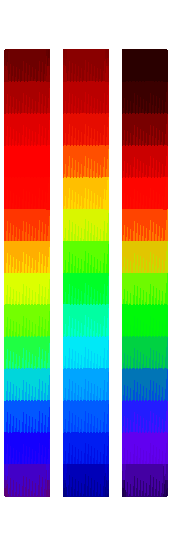

```mathematica
GetCplxData[fname_,dir_]:=Module[{dataRaw},
dataRaw=Import[FileNameJoin[{dir,fname}],"TSV"];
ToExpression[StringReplace[#,{"im"->"*I","e"->"*10^"}]&/@dataRaw]]

GetRealData[fname_,dir_]:=Import[FileNameJoin[{dir,fname}],"TSV"]

RgbSpec[x_]:=Blend[{{0,RGBColor[19/50,0,2/5]},{3/40,RGBColor[19/100,0,1]},{3/20,Blue},{11/40,Cyan},{13/40,Green},{1/2,Yellow},{13/20,Red},{4/5,Red},{1,RGBColor[7/20,0,0]}},x]
RgbSpecCustom[x_]:=Blend[{{-0.05,RGBColor[0/50,0,1/5]},{0.10,Blue},{0.35,Cyan},{0.5,Green},{0.63,Yellow},{0.75,Orange},{0.8,Red},{1.05,RGBColor[7/20,0,0]}},x]
VisibleSpectrum[x_]:=ColorData["VisibleSpectrum"][Rescale[x,{0,1},{380,780}]]

PlotColorFun[fun_]:=DensityPlot[y,{x,0,1},{y,0,1},ColorFunction->(fun[#]&),ColorFunctionScaling->False,AspectRatio->10/1,FrameTicks->{{Automatic,None},{None,None}},Frame->Automatic,PlotRangePadding->None]
GraphicsRow[{PlotColorFun[RgbSpec],PlotColorFun[RgbSpecCustom],PlotColorFun[VisibleSpectrum]}]
```

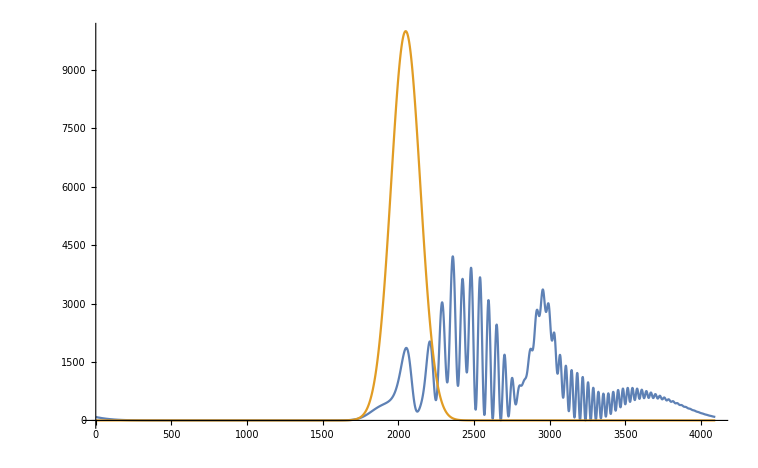

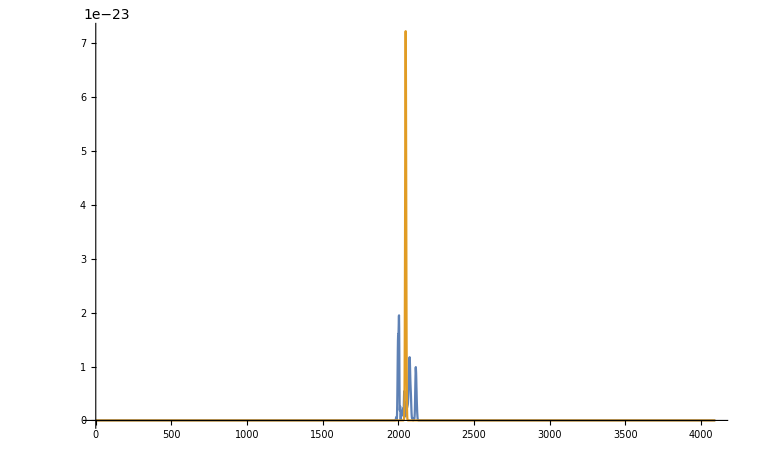

-Graphics-

-Graphics-

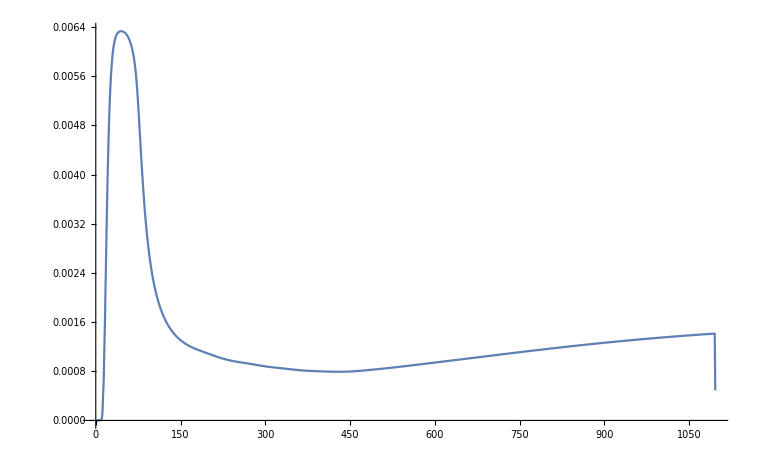

```mathematica
dir = "/home/s_koval/Code/julia/fl/out";

u0=Flatten@GetRealData["u0.tsv",dir];
u1=Flatten@GetRealData["u1.tsv",dir];
u0w=Flatten@GetRealData["U0.tsv",dir];
u1w=Flatten@GetRealData["U1.tsv",dir];
u=GetRealData["u_plot.tsv",dir];
ulog=GetRealData["u_log_plot.tsv",dir];
uwlog=GetRealData["U_log_plot.tsv",dir];
steps=Flatten@GetRealData["steps.tsv",dir];

uplot = ListPlot[{u1, u0},Joined->True,PlotRange->Full]
uwplot=ListPlot[{u1w, u0w},Joined->True, PlotRange->Full]
(*u3Dplot=ListPlot3D[u, PlotRange->Full, ColorFunction->Function[{x,y,z},RgbSpecCustom[z]]]*)
u3Dlogplot=ListDensityPlot[ulog, PlotRange->Full, ColorFunction->(RgbSpecCustom[#]&)]
uw3Dlogplot=ListDensityPlot[uwlog, PlotRange->Full,ColorFunction->(RgbSpecCustom[#]&)]
stepsplot =ListPlot[steps, Joined->True, PlotRange->Full]
```

10

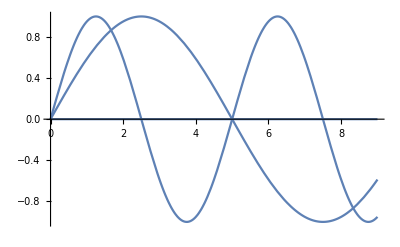

```mathematica
n = 10

Plot[Table[Sin[2 π m k/n],{m,0,2}],{k,0,n-1}]
```

```mathematica
b2=-11.830;
b3=8.1038 10^-2;
b4=-9.5205*10^-5;
b5=2.0737 10^-7;
b6=-5.3943*10^-10;
b7=1.3486 10^-12;
b8=-2.5495*10^-15;
b9=3.0524 10^-18;
b10=-1.7140*10^-21;
{b2,b3,b4,b5,b6,b7,b8,b9,b10}*Table[(π/10 10^4)^k,{k,2,10}]
```

{-1.16757×10^8,2.51269×10^9,-9.27383×10^9,6.34593×10^10,-5.18602×10^11,4.07317×10^12,-2.4191×10^13,9.09893×10^13,-1.60513×10^14}

```mathematica
ListDensityPlot[uwlog, PlotRange->Full,ColorFunction->(RgbSpecCustom[#]&)]
```

-Graphics-

```mathematica
ListDensityPlot[ulog, PlotRange->Full, ColorFunction->(RgbSpecCustom[#]&)]
```

-Graphics-

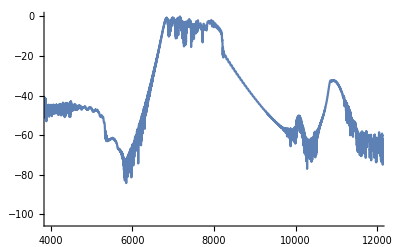

```mathematica
up=Sqrt[u1w]/Max[Sqrt[u1w]];
ListPlot[10Log10[up], Joined->True,PlotRange->{All,All}]
```

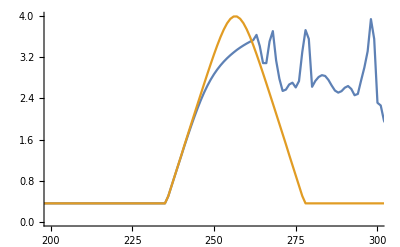

```mathematica
ListPlot[{ulog[[200]],ulog[[1]]}, Joined->True,PlotRange->{{200,300},All}]
```